```mathematica
Manipulate[
Module[{w1,w2,h1,h2,L,H,θ1,z1,θ2,θ3,reactions,RAx,RAy,RE,scale,colC,colT},
w1=5;w2=7;h1=3;h2=5;L=2*(w1+w2);H=h1+h2;

θ1=ArcTan[h1/(0.33*w2)];z1=√(h1^2+(0.67*w2)^2);θ2=ArcTan[h1/(0.67*w2)];θ3=ArcTan[(h1+h2)/w1];

reactions=Quiet@Solve[{
rax+FA*Cos[θ1]==0,
z1*(-FA)+2*(w1+w2)*re+(w1+w2)*(-FB)==0,
ray-FA*Sin[θ1]+re-FB==0
},{rax,ray,re}][[1]];
RAx=rax/.reactions;RAy=ray/.reactions;RE=re/.reactions;

scale[F_]:=1.5+5*Rescale[Abs@F,{0,10}];
colC=RGBColor[0,0.6,0];colT=Magenta;

Graphics[{
{Thick,Line[{{w2,0},{0.67*w2,h1}}],Line[{{w2,0},{w1+w2,H}}],Line[{{2*w1+w2,0},{L-0.67*w2,h1}}],Line[{{2*w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,0},{w1+w2,H}}]},
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{L,0},{w1+w2,H}}]},

Line[{{0,-0.35*h1},{L,-0.35*h1}}],Line[{{#,-0.25*h1},{#,-0.45*h1}}]&/@{w2,w2+w1,w2+2*w1,L},
Text[Style[Subscript[Style["w",Italic],#1],17,Background->White],{#2,-0.35*h1}]&@@@{{2,0.5*w2},{1,w2+0.5*w1},{1,w2+1.5*w1},{2,1.5*w2+2*w1}},

Line[{{-0.2*w1,0},{-0.2*w1,H}}],Line[{{-0.3*w1,#},{-0.1*w1,#}}]&/@{0,h1,H},
Text[Style[Subscript[Style["h",Italic],#1],17,Background->White],{-0.2*w1,#2}]&@@@{{1,0.5*h1},{2,h1+0.5*h2}},

Text[Style[Subscript[Style["θ",Italic],#1],17],{#2,0},1.2*#3]&@@@{{1,w2,{2,-1}},{1,2*w1+w2,{-2,-1}},{2,0,{-3.5,-1}},{2,L,{3.5,-1}},{3,w2,{-2,-1}},{3,2*w1+w2,{2,-1}}},

{Thick,colC,Arrowheads@{{-0.045,0.1},{0.045,0.9}},Arrow[{{0,0},{0.67*w2,h1}}],Arrow[{{0.67*w2,h1},{w1+w2,H}}],Arrow[{{w1+w2,H},{2*w1+1.33*w2,h1}}],Arrow[{{2*w1+1.33*w2,h1},{L,0}}]},

{Thick,colT,Arrowheads@{{0.045,0.4},{-0.045,0.6}},Arrow[{{0,0},{w2,0}}],Arrow[{{w2,0},{w1+w2,0}}],Arrow[{{0.67*w2,h1},{w2,0}}],Arrow[{{w2,0},{w1+w2,H}}],Arrow[{{w1+w2,0},{2*w1+w2,0}}],Arrow[{{2*w1+w2,0},{L,0}}]},

Text[Framed[Style[Subscript[Style["F",Italic],#1],17],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{{1,{0.67*w2,h1}/2},{8,{w2/2,0}},{2,{0.8*w2+w1/2,h1+h2/2}},{9,{0.67*w2+0.33*w2/2,h1/2}},{10,{w2+w1/2,(h1+h2)/2}},{11,{w1+w2,(h1+h2)/2}},{12,{1.5*w1+w2,(h1+h2)/2}},{3,{2*w1+0.85*w2,h1+h2/2}},{4,{2*w1+1.67*w2,h1/2}},{13,{2*w1+w2+0.33*w2/2,h1/2}},{5,{2*w1+1.5*w2,0}},{6,{1.5*w1+w2,0}},{7,{w1/2+w2,0}}},

Text[Framed[Style[Row@{" ",#1," "},14],Background->White,RoundingRadius->15],#2]&@@@{
{"A",{0,0}},{"B",{0.67*w2,h1}},{"C",{w1+w2,H}},{"D",{2*w1+1.33*w2,h1}},{"E",{L,0}},{"F",{2*w1+w2,0}},{"G",{w1+w2,0}},{"H",{w2,0}}},

{Thick,Arrowheads@0.045,Blue,
If[FA≠0,Arrow[{{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.9*0.67*w2,1.1*h1}}]],
If[FB≠0,Arrow[{{w1+w2,h1+h2+scale[FB]},{w1+w2,1.05*(h1+h2)}}]],
If[#1≠0,Text[Style[Subscript[Style["F",Italic],#1],18,Blue],#2,#3]]&@@@{{"B",{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.,-1}},{"C",{w1+w2,h1+h2+scale[FB]},{0,-1.5}}},
If[RAy≠0,Arrow[{{0,-scale[RAy]},{0,-0.1*h1}}]],If[RAx≠0,Arrow[{{-scale[RAx],0},{-0.1*w1,0}}]],
If[#1≠0,Text[Style[Subscript[Style["R",Italic],Row@{"A,",#1}],18],#2,#3]]&@@@{{"x",{-scale[RAx],0},{1.1,0}},{"y",{0,-scale[RAy]},{0,1.5}}},
If[RE≠0,Arrow[{{2*(w1+w2),-scale[RE]},{2*(w1+w2),-0.1*h1}}]],
If[RE≠0,Text[Style[Subscript[Style["R",Italic],"E"],18],{2*(w1+w2),-scale[RE]},{0,1.5}]]}
},ImageSize->{600,425}]
],
Grid@{{
"point load forces (kN):",
Control[{{FA,2,"diagonal"},0,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FB,5,"vertical"},0,10,0.1,Appearance->"Labeled",ImageSize->Small}]
}}
]
```

```mathematica
Manipulate[
Module[{w1,w2,h1,h2,L,H,θ1,z1,θ2,θ3,reactions,RAx,RAy,RE,scale,colC,colT},
w1=5;w2=7;h1=3;h2=5;L=2*(w1+w2);H=h1+h2;

θ1=ArcTan[h1/(0.33*w2)];z1=√(h1^2+(0.67*w2)^2);θ2=ArcTan[h1/(0.67*w2)];θ3=ArcTan[(h1+h2)/w1];

reactions=Quiet@Solve[{
rax+FA*Cos[θ1]==0,
z1*(-FA)+2*(w1+w2)*re+(w1+w2)*(-FB)==0,
ray-FA*Sin[θ1]+re-FB==0
},{rax,ray,re}][[1]];
RAx=rax/.reactions;RAy=ray/.reactions;RE=re/.reactions;

scale[F_]:=1.5+5*Rescale[Abs@F,{0,10}];
colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Graphics[{
{Thick,Line[{{w2,0},{0.67*w2,h1}}],Line[{{w2,0},{w1+w2,H}}],Line[{{2*w1+w2,0},{L-0.67*w2,h1}}],Line[{{2*w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,0},{w1+w2,H}}]},
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{L,0},{w1+w2,H}}]},

Line[{{0,-0.35*h1},{L,-0.35*h1}}],Line[{{#,-0.25*h1},{#,-0.45*h1}}]&/@{w2,w2+w1,w2+2*w1,L},
Text[Style[Subscript[Style["w",Italic],#1],17,Background->White],{#2,-0.35*h1}]&@@@{{2,0.5*w2},{1,w2+0.5*w1},{1,w2+1.5*w1},{2,1.5*w2+2*w1}},

Line[{{-0.2*w1,0},{-0.2*w1,H}}],Line[{{-0.3*w1,#},{-0.1*w1,#}}]&/@{0,h1,H},
Text[Style[Subscript[Style["h",Italic],#1],17,Background->White],{-0.2*w1,#2}]&@@@{{1,0.5*h1},{2,h1+0.5*h2}},

Text[Style[Subscript[Style["θ",Italic],#1],17],{#2,0},1.2*#3]&@@@{{1,w2,{2,-1}},{1,2*w1+w2,{-2,-1}},{2,0,{-3.5,-1}},{2,L,{3.5,-1}},{3,w2,{-2,-1}},{3,2*w1+w2,{2,-1}}},

{Thick,colC,Arrowheads@{{-0.045,0.1},{0.045,0.9}},Arrow[{{0,0},{0.67*w2,h1}}],Arrow[{{0.67*w2,h1},{w1+w2,H}}],Arrow[{{w1+w2,H},{2*w1+1.33*w2,h1}}],Arrow[{{2*w1+1.33*w2,h1},{L,0}}]},

{Thick,colT,Arrowheads@{{0.045,0.4},{-0.045,0.6}},Arrow[{{0,0},{w2,0}}],Arrow[{{w2,0},{w1+w2,0}}],Arrow[{{0.67*w2,h1},{w2,0}}],Arrow[{{w2,0},{w1+w2,H}}],Arrow[{{w1+w2,0},{2*w1+w2,0}}],Arrow[{{2*w1+w2,0},{L,0}}]},

Text[Framed[Style[Subscript[Style["F",Italic],#1],17],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{{1,{0.67*w2,h1}/2},{8,{w2/2,0}},{2,{0.8*w2+w1/2,h1+h2/2}},{9,{0.67*w2+0.33*w2/2,h1/2}},{10,{w2+w1/2,(h1+h2)/2}},{11,{w1+w2,(h1+h2)/2}},{12,{1.5*w1+w2,(h1+h2)/2}},{3,{2*w1+0.85*w2,h1+h2/2}},{4,{2*w1+1.67*w2,h1/2}},{13,{2*w1+w2+0.33*w2/2,h1/2}},{5,{2*w1+1.5*w2,0}},{6,{1.5*w1+w2,0}},{7,{w1/2+w2,0}}},

Text[Framed[Style[Row@{" ",#1," "},14],Background->White,RoundingRadius->15],#2]&@@@{
{"A",{0,0}},{"B",{0.67*w2,h1}},{"C",{w1+w2,H}},{"D",{2*w1+1.33*w2,h1}},{"E",{L,0}},{"F",{2*w1+w2,0}},{"G",{w1+w2,0}},{"H",{w2,0}}},

{Thick,Arrowheads@0.045,Blue,
If[FA≠0,Arrow[{{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.9*0.67*w2,1.1*h1}}]],
If[FB≠0,Arrow[{{w1+w2,h1+h2+scale[FB]},{w1+w2,1.05*(h1+h2)}}]],
If[#1≠0,Text[Style[Subscript[Style["F",Italic],#1],18,Blue],#2,#3]]&@@@{{"B",{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.,-1}},{"C",{w1+w2,h1+h2+scale[FB]},{0,-1.5}}},
If[RAy≠0,Arrow[{{0,-scale[RAy]},{0,-0.1*h1}}]],If[RAx≠0,Arrow[{{-scale[RAx],0},{-0.1*w1,0}}]],
If[#1≠0,Text[Style[Subscript[Style["R",Italic],Row@{"A,",#1}],18],#2,#3]]&@@@{{"x",{-scale[RAx],0},{1.1,0}},{"y",{0,-scale[RAy]},{0,1.5}}},
If[RE≠0,Arrow[{{2*(w1+w2),-scale[RE]},{2*(w1+w2),-0.1*h1}}]],
If[RE≠0,Text[Style[Subscript[Style["R",Italic],"E"],18],{2*(w1+w2),-scale[RE]},{0,1.5}]]}
},ImageSize->{600,425}]
],
Grid@{{
"point load forces (kN):",
Control[{{FA,2,"diagonal"},0,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FB,5,"vertical"},0,10,0.1,Appearance->"Labeled",ImageSize->Small}]
}}
]
```

```mathematica
Manipulate[
Module[{w1,w2,h1,h2,L,H,δ,θ1,z1,θ2,θ3,reactions,RAx,RAy,RE,scale,colC,colT},
w1=5;w2=7;h1=3;h2=5;L=2*(w1+w2);H=h1+h2;δ=3;

θ1=ArcTan[h1/(0.33*w2)];z1=√(h1^2+(0.67*w2)^2);θ2=ArcTan[h1/(0.67*w2)];θ3=ArcTan[(h1+h2)/w1];

reactions=Quiet@Solve[{
rax+FA*Cos[θ1]==0,
z1*(-FA)+2*(w1+w2)*re+(w1+w2)*(-FB)==0,
ray-FA*Sin[θ1]+re-FB==0
},{rax,ray,re}][[1]];
RAx=rax/.reactions;RAy=ray/.reactions;RE=re/.reactions;

scale[F_]:=1.5+5*Rescale[Abs@F,{0,10}];
colC=RGBColor[0,0.6,0];colT=Magenta;

Graphics[{
{Thick,Line[{{w2,0},{0.67*w2,h1}}],Line[{{w2,0},{w1+w2,H}}],Line[{{2*w1+w2,0},{L-0.67*w2,h1}}],Line[{{2*w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,0},{w1+w2,H}}]},
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{L,0},{w1+w2,H}}]},

{Thick,Arrowheads@{{-0.04,0.1},{0.04,0.9}},Arrow[{{0,0},{0.67*w2,h1}}],Arrow[{{0.67*w2,h1},{w1+w2,H}}],Arrow[{{w1+w2,H},{2*w1+1.33*w2,h1}}],Arrow[{{2*w1+1.33*w2,h1},{L,0}}]},

{Thick,Arrowheads@{{0.04,0.4},{-0.04,0.6}},Arrow[{{0,0},{w2,0}}],Arrow[{{w2,0},{w1+w2,0}}],Arrow[{{0.67*w2,h1},{w2,0}}],Arrow[{{w2,0},{w1+w2,H}}],Arrow[{{w1+w2,0},{2*w1+w2,0}}],Arrow[{{2*w1+w2,0},{L,0}}]},

Text[Framed[Style[Subscript[Style["F",Italic],#1],17],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{{1,{0.67*w2,h1}/2},{8,{w2/2,0}},{2,{0.8*w2+w1/2,h1+h2/2}},{9,{0.67*w2+0.33*w2/2,h1/2}},{10,{w2+w1/2,(h1+h2)/2}},{11,{w1+w2,(h1+h2)/2}},{12,{1.5*w1+w2,(h1+h2)/2}},{3,{2*w1+0.85*w2,h1+h2/2}},{4,{2*w1+1.67*w2,h1/2}},{13,{2*w1+w2+0.33*w2/2,h1/2}},{5,{2*w1+1.5*w2,0}},{6,{1.5*w1+w2,0}},{7,{w1/2+w2,0}}},

Text[Framed[Style[Row@{" ",#1," "},14],Background->White,RoundingRadius->15],#2]&@@@{
{"A",{0,0}},{"B",{0.67*w2,h1}},{"C",{w1+w2,H}},{"D",{2*w1+1.33*w2,h1}},{"E",{L,0}},{"F",{2*w1+w2,0}},{"G",{w1+w2,0}},{"H",{w2,0}}},

(*{Thick,Arrowheads@0.045,Blue,
Arrow[{{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.9*0.67*w2,1.1*h1}}],
Arrow[{{w1+w2,h1+h2+scale[FB]},{w1+w2,1.05*(h1+h2)}}],
Text[Style[Subscript[Style["F",Italic],#1],18,Blue],#2,#3]&@@@{{"B",{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.,-1}},{"C",{w1+w2,h1+h2+scale[FB]},{0,-1.5}}},
Arrow[{{0,-scale[RAy]},{0,-0.1*h1}}],
Arrow[{{-scale[RAx],0},{-0.1*w1,0}}],
Text[Style[Subscript[Style["R",Italic],Row@{"A,",#1}],18],#2,#3]&@@@{{"x",{-scale[RAx],0},{1.1,0}},{"y",{0,-scale[RAy]},{0,1.5}}},
Arrow[{{2*(w1+w2),-scale[RE]},{2*(w1+w2),-0.1*h1}}],
Text[Style[Subscript[Style["R",Italic],"E"],18],{2*(w1+w2),-scale[RE]},{0,1.5}]}*)
{Thick,Arrowheads@0.045,
Arrow[{{0.67*w2-δ*Cos[θ1],h1+δ*Sin[θ1]},{0.95*0.67*w2,1.15*h1}}],
Arrow[{{w1+w2,h1+h2+δ},{w1+w2,1.07*(h1+h2)}}],
Text[Style[Subscript[Style["F",Italic],#1],18],#2,#3]&@@@{{"B",{0.67*w2-δ*Cos[θ1],h1+δ*Sin[θ1]},{0.5,-1}},{"C",{w1+w2,h1+h2+δ},{0,-1.5}}},
Arrow[{{0,-δ},{0,-0.15*h1}}],
Arrow[{{-δ,0},{-0.15*w1,0}}],
Text[Style[Subscript[Style["R",Italic],Row@{"A,",#1}],18],#2,#3]&@@@{{"x",{-δ,0},{1.1,0}},{"y",{0,-δ},{0,1.5}}},
Arrow[{{2*(w1+w2),-δ},{2*(w1+w2),-0.15*h1}}],
Text[Style[Subscript[Style["R",Italic],"E"],18],{2*(w1+w2),-δ},{0,1.5}]}
},ImageSize->600]
],
Grid@{{
"point load forces (kN):",
Control[{{FA,2,"diagonal"},0,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FB,5,"vertical"},0,10,0.1,Appearance->"Labeled",ImageSize->Small}]
}}
]
```

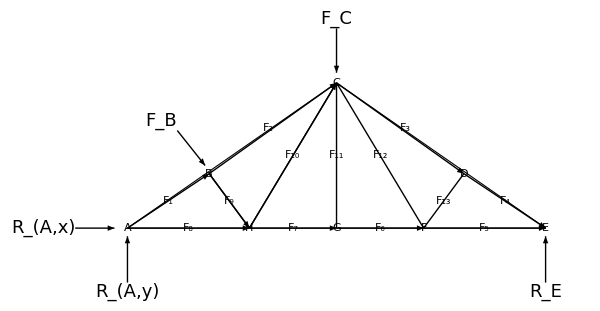

```mathematica
Module[{w1,w2,h1,h2,L,H,δ,θ1,z1,θ2,θ3,reactions,RAx,RAy,RE,scale,colC,colT},
w1=5;w2=7;h1=3;h2=5;L=2*(w1+w2);H=h1+h2;δ=3;

θ1=ArcTan[h1/(0.33*w2)];z1=√(h1^2+(0.67*w2)^2);θ2=ArcTan[h1/(0.67*w2)];θ3=ArcTan[(h1+h2)/w1];

Graphics[{
{Thick,Line[{{w2,0},{0.67*w2,h1}}],Line[{{w2,0},{w1+w2,H}}],Line[{{2*w1+w2,0},{L-0.67*w2,h1}}],Line[{{2*w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,0},{w1+w2,H}}]},
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{L,0},{w1+w2,H}}]},

{Thick,Arrowheads@{{-0.04,0.1},{0.04,0.9}},Arrow[{{0,0},{0.67*w2,h1}}],Arrow[{{0.67*w2,h1},{w1+w2,H}}],Arrow[{{w1+w2,H},{2*w1+1.33*w2,h1}}],Arrow[{{2*w1+1.33*w2,h1},{L,0}}],Arrow[{{0.67*w2,h1},{w2,0}}]},

{Thick,Arrowheads@{{0.04,0.4},{-0.04,0.6}},Arrow[{{0,0},{w2,0}}],Arrow[{{w2,0},{w1+w2,0}}],Arrow[{{w2,0},{w1+w2,H}}],Arrow[{{w1+w2,0},{2*w1+w2,0}}],Arrow[{{2*w1+w2,0},{L,0}}]},

Text[Framed[Style[Subscript[Style["F",Italic],#1],17],Background->White,FrameStyle->None,FrameMargins->None],#2]&@@@{{1,{0.67*w2,h1}/2},{2,{0.8*w2+w1/2,h1+h2/2}},{3,{2*w1+0.85*w2,h1+h2/2}},{4,{2*w1+1.67*w2,h1/2}},{5,{2*w1+1.5*w2,0}},{6,{1.5*w1+w2,0}},{7,{w1/2+w2,0}},{8,{w2/2,0}},{9,{0.67*w2+0.33*w2/2,h1/2}},{10,{w2+w1/2,(h1+h2)/2}},{11,{w1+w2,(h1+h2)/2}},{12,{1.5*w1+w2,(h1+h2)/2}},{13,{2*w1+w2+0.33*w2/2,h1/2}}},

Text[Framed[Style[Row@{" ",#1," "},16],Background->White,RoundingRadius->15,FrameMargins->Small],#2]&@@@{
{"A",{0,0}},{"B",{0.67*w2,h1}},{"C",{w1+w2,H}},{"D",{2*w1+1.33*w2,h1}},{"E",{L,0}},{"F",{2*w1+w2,0}},{"G",{w1+w2,0}},{"H",{w2,0}}},

{Thick,Arrowheads@0.045,
Arrow[{{0.67*w2-δ*Cos[θ1],h1+δ*Sin[θ1]},{0.95*0.67*w2,1.15*h1}}],
Arrow[{{w1+w2,h1+h2+δ},{w1+w2,1.07*(h1+h2)}}],
Text[Style[Subscript[Style["F",Italic],#1],18],#2,#3]&@@@{{"B",{0.67*w2-δ*Cos[θ1],h1+δ*Sin[θ1]},{0.5,-1}},{"C",{w1+w2,h1+h2+δ},{0,-1.5}}},
Arrow[{{0,-δ},{0,-0.15*h1}}],
Arrow[{{-δ,0},{-0.15*w1,0}}],
Text[Style[Subscript[Style["R",Italic],Row@{"A,",#1}],18],#2,#3]&@@@{{"x",{-δ,0},{1.1,0}},{"y",{0,-δ},{0,1.5}}},
Arrow[{{2*(w1+w2),-δ},{2*(w1+w2),-0.15*h1}}],
Text[Style[Subscript[Style["R",Italic],"E"],18],{2*(w1+w2),-δ},{0,1.5}]}
},ImageSize->600]
]
```